## Topic

### Definition / Theorem

This is text.

#### Example

## Limit of a complex function

```mathematica
ClearAll[g]
g[z_]:=(z+2)/(z-1)
Limit[g[z],z->Infinity]
Apart[g[z],z]
(*Abs[.99+.01I]*)
Abs[g[1.01]-1]
```

1

1+3/(-1+z)

300.

## Gamma Function

```mathematica
ClearAll[gamma]
(*gamma[s_]:=Integrate[x^(s-1)ⅇ^-x,{x,0,Infinity}]*)
gamma[x_]:=Integrate[t^(x-1)ⅇ^-t,{t,0,Infinity}]
gamma2[x_]:=1/x Integrate[t^x ⅇ^-t,{t,0,Infinity}]
gamma[t]//TraditionalForm
Log[10.,Gamma[70]]
```

Integrate::idiv: Integral of ⅇ^-t t^(-1+t) does not converge on {0,∞}.

∫_0^∞ ⅇ^-t t^(t-1)ⅆt

98.2333

2.54926

2.54926

120

2.54926

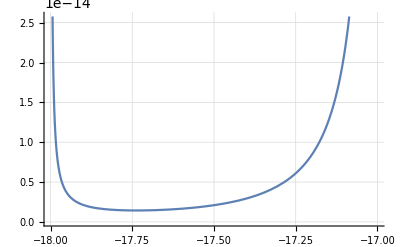

```mathematica
gamma[3.25]//N
gamma2[3.25]//N
gamma[6]
Gamma[3.25]//N
Plot[Gamma[x],{x,-18,-17},GridLines->Automatic]
```

```mathematica
gamma[z_]:=Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]
gamma[z]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[t^(z-1)-ⅇ^-t,{t,0,Infinity}]+Integrate[ⅇ^-t(z-1)t^(z-2),{t,0,Infinity}]
```

Integrate::idiv: Integral of -ⅇ^-t+t^(-1+z) does not converge on {0,∞}.

ConditionalExpression[Gamma[z]+∫_0^∞ (-ⅇ^-t+t^(-1+z))ⅆt, Re[z]>1]

```mathematica
1/6-5/66
```

1/11

```mathematica
D[ -x Cos[x]+Sin[x],{x,1}]//FullSimplify
```

x Sin[x]

```mathematica
Integrate[Gamma[z],z]
```

∫Gamma[z]ⅆz

```mathematica
Integrate[Exp[-a u^2],{u,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √a), Re[a]>0]

```mathematica
Integrate[ⅇ^((z-1)Log[t]-t),{t,0,Infinity}]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
Gamma[I]//N
```

-0.15495-0.498016 ⅈ

```mathematica
Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]/.z:>5
```

24

```mathematica
u[t_]:=t^(z-1)
u[t_]:=1
v[t_]:=-ⅇ^-t
```

```mathematica
Integrate[u[t]D[v[t],{t,1}],{t,0,Infinity}]

Integrate[v[t]D[u[t],{t,1}],{t,0,Infinity}]
```

1

0

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
D[ⅇ^-t t^(x-1),{x,3}]
```

```mathematica
Gamma'''[x]
Integrate[ⅇ^-t t^(-1+x) Log[t]^3,{x,0,Infinity}]
```

Gamma[x] PolyGamma[0,x]^3+3 Gamma[x] PolyGamma[0,x] PolyGamma[1,x]+Gamma[x] PolyGamma[2,x]

ConditionalExpression[-(ⅇ^-t Log[t]^2)/t, Re[Log[t]]<0]

```mathematica
240*.35
```

84.

```mathematica
Solve[{Gamma'[x]==1},x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Gamma[x] PolyGamma[0,x]==1},x]

```mathematica
f[y_]:=Integrate[x Cos[x],x]/.x:>y
f[π]-f[0]
```

-2

```mathematica
Integrate[x Cos[x],{x,0,π}]
```

-2

```mathematica
Table[Residue[Gamma[z],{z,-k}],{k,1,7}]
```

{-1,1/2,-1/6,1/24,-1/120,1/720,-1/5040}